```mathematica
(*将常数吸收到解中可得如下等价问题，f[x,y]表示 {du/dt,dv/dt},g[t]是此问题的解*）
```

```mathematica
f[{x_,y_}]:={-2000*x+999.75*y,x-y};
g[t_]:={-1.499875*E^(-0.5*t)+0.499875*E^(-2000.5*t),-2.99975*E^(-0.5*t)-0.00025*E^(-2000.5*t)}
```

```mathematica
Eigenvalues[{{-2000,999.75},{1,-1}}]
```

{-2000.5,-0.5}

```mathematica
(*根据课本P400页对四阶显式Runge-Kutta方法绝对稳定性的讨论，此时步长需有h<2.785/2000.5 约为0.001才保证稳定性*)
```

```mathematica
(*数值实验发现h较大时无法得到正确的数值解*）
```

```mathematica
(*用classical 四级显式Runge-Kutta迭代法求解，取步长为0.001*）
```

```mathematica
f[{x_,y_}]:={x+2y,3x+2y};
h=0.02;
y[0]={-1,-3};
For[i=0,i<20000,i++,K1=f[y[i]];K2=f[y[i]+1/2*h*K1];K3=f[y[i]+1/2*h*K2];
K4=f[y[i]+h*K3];
y[i+1]=y[i]+1/6*h*(K1+2*K2+2*K3+K4)]
```

```mathematica
(*由下图可见，g[t]的第一个分量初值虽为-1,但由于E^(-2000.5t)的指数项，其很快衰减到0而E^(-0.5t)的系数-1.5起主要作用*)
```

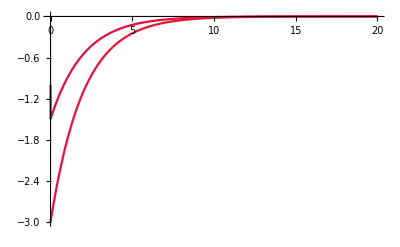

```mathematica
Plot[{g[t][[1]],g[t][[2]]},{t,0,20},PlotRange->All,ColorFunction->Hue]
```

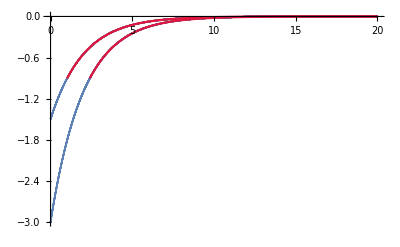

```mathematica
(*由下图可见，数值解与解析结果符合甚好*）
```

```mathematica
(*二级四阶隐式格式，其中K1,K2可通过求解线性方程组得到*)
```

```mathematica
h=0.1;
For[i=0,i<200,i++,K1=0;K2=0;eq=NSolve[{{a,b}=={(-500. a+249.9375 b+77.35026918962573 c-38.665465811164175 d) h,1/12 (3 a-3 b-(-3+2 √3) (c-d)) h}+f[y[i]],{c,d}=={(-1077.3502691896256 a+538.5404658111642 b-500. c+249.93749999999997 d) h,1/12 ((3+2 √3) a-3 b-2 √3 b+3 c-3 d) h}+f[y[i]]},{a,b,c,d}];K1=({{a,b},{c,d}}/.eq[[1]])[[1]];
K2=({{a,b},{c,d}}/.eq[[1]])[[2]];
y[i+1]=y[i]+1/2*h*(K1+K2);]
```

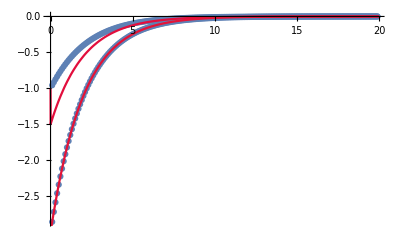

```mathematica
(*结果分析：下图中蓝色的点表示离散化后的数值解，由真解的第一分量在t=0处从-1跳到-1.5可知，初值的第一分量为-1具有欺骗性，它使得真解在0处导数值很大，而差分方法对这种情形无能为力*）
```